## Styling

```mathematica
dir=NotebookDirectory[]
```

/home/nicolas/git/articles/electronic_wavefunctions/

```mathematica
(* Thickness *)
th=0.003;
```

```mathematica
(*Styling of the text*)
st=Directive[FontSize->15,FontFamily->"CMU Serif"];
stylize[text_]:=Style[text,st];
```

```mathematica
BostonBlue=RGBColor["#00688B"];
comp=RGBColor["#8B2300"];
```

```mathematica
SetOptions[ListPlot,Frame->True,FrameStyle->st,PlotRange->All,PlotStyle->Black];
```

## Utility functions

```mathematica
(* string substitution *)
Sub[rule_,init_String,l_Integer]:=Nest[StringReplace[#,rule]&,init,l]
```

```mathematica
(* Height (integrated arrow field), can also be seen as the mode k=0 of the Fourier transform of the sequence of arrows *)
Heights[arrows_]:=Table[Total[arrows[[;;N]]],{N,1,Length[arrows]}];
```

```mathematica
(* maximum of the height distribution *)
MaxHeights[heights_]:=Block[{absheights=Abs[heights]},Table[Max[absheights[[;;N]]],{N,1,Length[heights]}]];
```

```mathematica
(* for a string of an even number of A and B, replace every couple by the corresponding arrow *)
ToArrowAlphabet[string_]:=StringReplace[string,{"AB"->"R","BA"->"L","AA"->"Ia","BB"->"Ib"}];
(* return the vector counting the number of arrows *)
ArrowCountVec[string_]:=StringCount[string,#]&/@{"R","L","Ia","Ib"};
```

```mathematica
(* periodic approximant of a sequence seq of two letters, in normal numbering *)
h[ρ_,seq_]:=Block[{jump,tbl,ar,n=StringLength[seq]},
jump[j_]:=If[StringTake[seq,{j}]=="B",1.,ρ];

(* nearest neighbour hopppings *)
tbl=Table[{i,i+1}->jump[i],{i,1,n-1}];
(* boundary conditions for the nearest neighbour hoppings *)
PrependTo[tbl,{1,n}->jump[n]];

(* transform to an array and construct the lower diagonal part *)
ar=SparseArray[tbl,{n,n}];
Normal[ar+ConjugateTranspose[ar]]
]
```

For the E=0 level to exist, we need an odd number of letters. But we also need the system to be bipartite for the wavefunction to be nonzero only on one site over two → open boundary conditions.

```mathematica
(* open approximant of a sequence seq of two letters, in normal numbering *)
ho[ρ_,seq_]:=Block[{jump,tbl,ar,n=StringLength[seq]},
jump[j_]:=If[StringTake[seq,{j}]=="B",1.,ρ];

(* nearest neighbour hopppings *)
tbl=Table[{i,i+1}->jump[i],{i,1,n-1}];

(* transform to an array and construct the lower diagonal part *)
ar=SparseArray[tbl,{n,n}];
Normal[ar+ConjugateTranspose[ar]]
]
```

```mathematica
(* sliding average *)
SlidingAverage[list_]:=Table[Mean[list[[;;N]]],{N,1,Length[list]}];
```

```mathematica
(* sliding harmonic average *)
SlidingHarmAverage[list_]:=Table[HarmonicMean[list[[;;N]]],{N,1,Length[list]}];
```

## Fibonacci heights

### Substitution rules

```mathematica
(* Fibonacci substitution *)
FiboSub[l_,C0_String]:=Sub[{"A"->"AB","B"->"A"},C0,l];
(* Fibonacci substitution, composed 3 times *)
FiboSub3[l_,C0_String]:=Sub[{"A"->"ABAAB","B"->"ABA"},C0,l];
ArrowSub[l_,C0_String]:=Sub[{"R"->"RILL","L"->"RILR","I"->"RILLR"},C0,l];
FiboArrows2[string_]:=StringPartition[string,1]/.{"R"->1,"L"->-1,"I"->0};
LocalEnvs={"RR","RI","LL","IL","LR"};
HeightCount[ArrowString_]:=StringCount[ArrowString,#]&/@LocalEnvs;
LocalEnvs2={"R","L","I"};
HeightCount2[ArrowString_]:=StringCount[ArrowString,#]&/@LocalEnvs2;
(* the field of arrows *)
FiboArrows[l_]:=StringPartition[FiboSub3[l,"AB"],2]/.{"AB"->1,"BA"->-1,"AA"->0};
FiboArrows2[l_]:=StringPartition[StringRotateLeft[FiboSub3[l,"AB"],1],2]/.{"AB"->1,"BA"->-1,"AA"->0};
```

### Height

```mathematica
n=6;
arrows=FiboArrows[n];
FiboHeights=Heights[arrows];
```

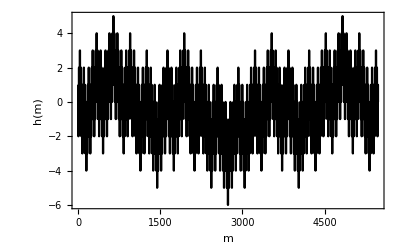

```mathematica
(* the height max grows logarithmically, and the height function goes to 0 arbitrarily far from the origin *)
ListPlot[FiboHeights,Joined->True,FrameLabel->stylize/@{"m","h(m)"}]
```

### Transmission coefficient

According to Beenakker, the transmission coefficient of the E=0 state can be written as
T_n = 4/(x_n+1/x_n)^2 où x_n=ψ_(2n)/ψ_0
Dans notre cas, cette formule devient
T_n=1/(cosh(κh(n)))^2 où κ=Logρ.

```mathematica
(* δh is the height difference between the first and last sites *)
Transmission[ρ_,δh_ ]:=1/Cosh[Log[ρ]δh]^2;
```

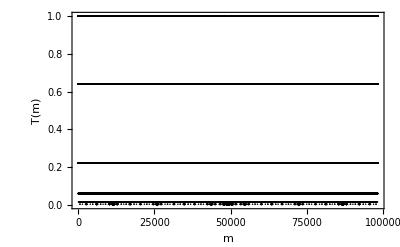

```mathematica
ρ=.5;
n=8;
arrows=FiboArrows[n];
FiboHeights=Heights[arrows];
FiboTr=Transmission[ρ,#]&/@FiboHeights;
(* the height max grows logarithmically, and the height function goes to 0 arbitrarily far from the origin *)
ListPlot[FiboTr,Joined->False,FrameLabel->stylize/@{"m","T(m)"},PlotRange->All]
```

```mathematica
Length[FiboHeights]
```

98209

```mathematica
(* sliding average *)
SlidingTrans[ρ_,heights_,L_]:=Table[Transmission[ρ,heights[[i0+L]]-heights[[i0]]],{i0,1,Length[heights]-L}];
```

```mathematica
Lrange=Range[10,Floor[Length[FiboHeights]/100]];
MeanSlide=Table[Mean[SlidingTrans[ρ,FiboHeights,L]],{L,Lrange}];
```

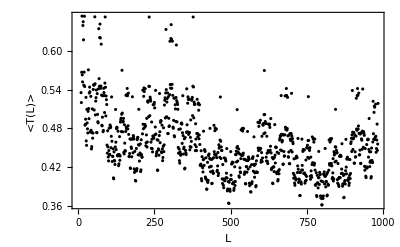

```mathematica
ListPlot[MapThread[{#1,#2}&,{Lrange,MeanSlide}],PlotRange->All,FrameLabel->stylize/@{"L","<T(L)>"}]
```

```mathematica
GeoMeanSlide=Table[GeometricMean[SlidingTrans[ρ,FiboHeights,L]],{L,Lrange}];
```

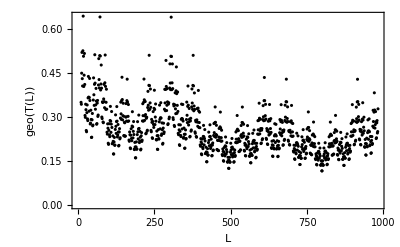

```mathematica
ListPlot[MapThread[{#1,#2}&,{Lrange,GeoMeanSlide}],PlotRange->All,FrameLabel->stylize/@{"L","geo(T(L))"}]
```

```mathematica
HarmonicMeanSlide=Table[HarmonicMean[SlidingTrans[ρ,FiboHeights,L]],{L,Lrange}];
```

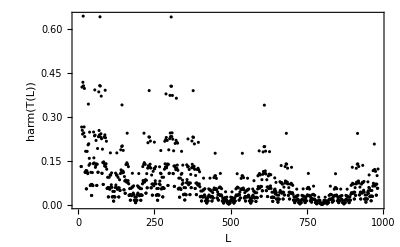

```mathematica
p=ListPlot[MapThread[{#1,#2}&,{Lrange,HarmonicMeanSlide}],PlotRange->All,FrameLabel->stylize/@{"L","harm(T(L))"}]
```

```mathematica
om[z_]:=(((1+z)^2+√((1+z)^4+4 z^2))/(2z))^2;
```

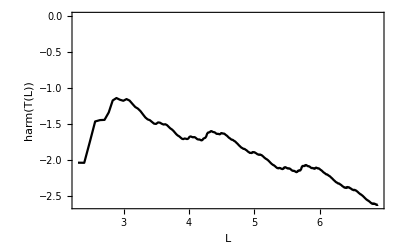

```mathematica
p=ListPlot[MapThread[{#1,#2}&,{Log@Lrange,Log@SlidingAverage@HarmonicMeanSlide}],Joined->True,PlotRange->All,FrameLabel->stylize/@{"L","harm(T(L))"}]
```

```mathematica
(* expected large distance behaviour for the harmonic mean transmission *)
HarmTr[ρ_,L_]:=1(L^(Log[om[ρ^2]/om[1]]/Log[GoldenRatio^6]))^-1;
```

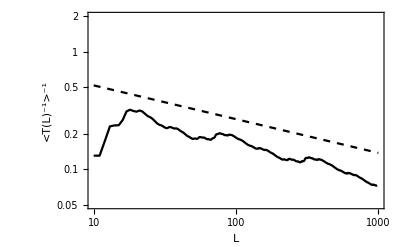

/home/nicolas/git/articles/electronic_wavefunctions/article/img/harmonic_mean_transmission.pdf

```mathematica
Show[LogLogPlot[HarmTr[ρ,L],{L,10,1000},PlotRange->{0.05,2},Frame->True,FrameStyle->st,PlotStyle->{Dashed,Black},FrameLabel->stylize/@{"L","<T(L)^-1>^-1"}],p]
Export[dir<>"article/img/harmonic_mean_transmission.pdf",%]
```

```mathematica
Harmo=SlidingHarmAverage[Transmission[ρ,# ]&/@FiboHeights];
```

$Aborted

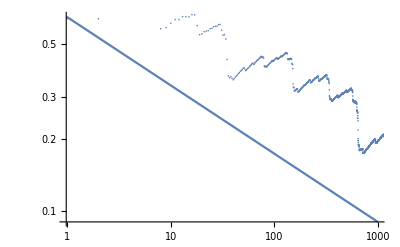

```mathematica
Show[LogLogPlot[HarmTr[ρ,L],{L,0,1000}],ListLogLogPlot[Harmo]]
```

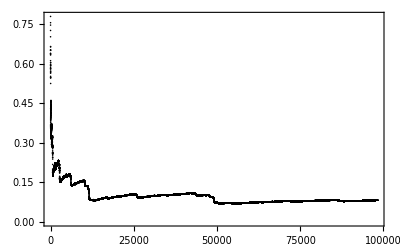

```mathematica
ListPlot[Harmo]
```

### Generalized inflation matrix

```mathematica
(* First we work with first neighbors local environments *)
LocalEnvs
```

{RR,RI,LL,IL,LR}

```mathematica
{"RL","LI","IR","II"}
```

{RL,LI,IR,II}

```mathematica
(* we obtain the inflation matrix for these environments straightforwardly by counting them *)
A=HeightCount/@(ArrowSub[1,#]&/@LocalEnvs);
Transpose[A]//MatrixForm
```

(0 | 0 | 1 | 1 | 1
2 | 2 | 2 | 2 | 2
2 | 2 | 0 | 1 | 1
2 | 2 | 2 | 2 | 2
1 | 2 | 2 | 2 | 1)

```mathematica
(* but weirdly, the matrix has eigenvalues in a different algebraic field *)
Eigensystem[Transpose[A]]
```

{{1/2 (7+√65),-1,-1,1/2 (7-√65),0},{{(4 (89+11 √65))/(5 (185+23 √65)),(8 (137+17 √65))/(5 (185+23 √65)),-(-655-81 √65)/(5 (185+23 √65)),(8 (137+17 √65))/(5 (185+23 √65)),1},{0,0,-1,0,1},{0,0,0,0,0},{(4 (-89+11 √65))/(5 (-185+23 √65)),(8 (-137+17 √65))/(5 (-185+23 √65)),-(655-81 √65)/(5 (-185+23 √65)),(8 (-137+17 √65))/(5 (-185+23 √65)),1},{-1,1,0,-1,1}}}

```mathematica
(* secondly, we look at local environments defined by "the letter at the right of the current site" *)
LocalEnvs2
```

{R,L,I}

```mathematica
(* the inflation matrix this time has eigenvalues in the expected field *)
A=HeightCount2/@(ArrowSub[1,#]&/@LocalEnvs2);
Transpose[A]//MatrixForm
Eigensystem[Transpose[A]]
```

(1 | 2 | 2
2 | 1 | 2
1 | 1 | 1)

{{2+√5,-1,2-√5},{{(2 (2+√5))/(3+√5),(2 (2+√5))/(3+√5),1},{-1,1,0},{(2 (-2+√5))/(-3+√5),(2 (-2+√5))/(-3+√5),1}}}

```mathematica
(* a dictionary from envs to indices *)
envs={"R","L","I"};
Idx=<|"R"->1,"L"->2,"I"->3|>;
inflatedEnvs=ArrowSub[1,#]&/@envs;
inflatedArrows=({0}~Join~FiboArrows2[#][[;;-2]])&/@inflatedEnvs;
inflatedHeights=Table[Total[#[[;;L]]],{L,1,Length[#]}]&/@inflatedArrows;
RowsHeights=MapThread[{#1,#2}&,{inflatedEnvs,inflatedHeights}];
(* construct the matrices *)
table0=Table[0,{i,1,3},{j,1,3}];
T2left=table0;
T20=table0;
T2right=table0;
(* a way of constructing the generalized matrices automatically *)
For[col=1,col≤3,col++,
{rows,heights}=RowsHeights[[col]];
rows=StringPartition[rows,1];
For[i=1,i≤Length[rows],i++,
h=heights[[i]];
row=Idx[rows[[i]]];
If[h==-1,
T2left[[row,col]]+=1,
If[h==0,
T20[[row,col]]+=1,
If[h==1,
T2right[[row,col]]+=1]]]
]
]
```

```mathematica
T2right//MatrixForm
```

(0 | 0 | 0
1 | 1 | 1
1 | 1 | 1)

```mathematica
T2left==Tleft
T2right==Tright
T20==T0
```

{{0,0,1},{0,0,0},{0,0,0}}==Tleft

{{0,0,0},{1,1,1},{1,1,1}}==Tright

{{1,2,1},{1,0,1},{0,0,0}}==T0

```mathematica
(* generalized inflation matrices for height dependent environments *)
T0={{1,2,1},{1,0,1},{0,0,0}};
Tright={{0,0,0},{1,1,1},{1,1,1}};
Tleft={{0,0,1},{0,0,0},{0,0,0}};
(* Legendre transform of the inflation matrix *)
T[z_]:=z T2left+T20+z^-1 T2right
(* Generating matrix of the height distribution *)
TT[z_]:=T[1/z].T[z]
```

```mathematica
(* Perron-Frobenius eigenvalue of TT is a perfect square: see height_distro_fibonacci.nb for more details *)
Simplify[(((1+z)^2+√((1+z)^4+4 z^2))/(2z))^2==(1+4 z+8 z^2+4 z^3+z^4+(1+z)^2 √(1+4 z+10 z^2+4 z^3+z^4))/(2 z^2),{z>0}]
```

True

```mathematica
FullSimplify[√((1+4 z+8 z^2+4 z^3+z^4+(1+z)^2 √(1+4 z+10 z^2+4 z^3+z^4))/(2 z^2)),{z>0}]
```

(√(1+4 z+8 z^2+4 z^3+z^4+(1+z)^2 √(1+z (4+z (10+z (4+z))))))/(√2 z)